```mathematica
K0[ρI0_,ρsi0_,β_,r_]:=ρI0 + (β/(β+r))*ρsi0
```

```mathematica
frinf[rinf_,ρssinf_,ρI0_,ρss0_, ρsi0_,β_,r_]:= 
ρI0 + (β/(β+r))*ρsi0 +(β/(β+r)) *( - Log[1-rinf]*4*ρssinf
+ Log[1-ρI0]*( 2* ρss0 - ρsi0) - Log[1-rinf] * (-2 ρss0 + ρsi0) )
```

```mathematica
findzero[rinf_,ρssinf_,ρI0_,ρss0_, ρsi0_,β_,r_]  := rinf - frinf[rinf,ρssinf,ρI0,ρss0, ρsi0,β,r]
```

```mathematica
β=0.004;
γ=1/40;
w=1/100;
κ=12/10000;
δ=2/100;
μ=15;
ρI0=0.01;
ρsi0=ρI0*μ*(1-ρI0);
ρss0=(μ/2)-ρsi0;
r=w+κ+γ;
```

```mathematica
Table[FindRoot[findzero[rinf,(μ/2)*(rinf^2),ρI0,ρss0, ρsi0,β,r] ,{rinf,0.5}][[1,2]],{β,0.002,0.06,0.002}]
```

{0.868598,0.00416987,-0.904471,0.762556,0.752947,0.746304,0.741437,0.737718,0.734783,0.732408,0.730447,0.7288,0.727398,0.726189,0.725136,0.724211,0.723392,0.722662,0.722006,0.721415,0.720878,0.72039,0.719942,0.719532,0.719153,0.718804,0.718479,0.718178,0.717897,0.717634}

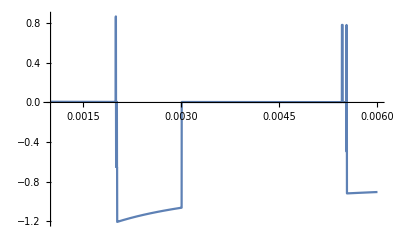

```mathematica
Plot[FindRoot[findzero[rinf,(μ/2)*(rinf^2),ρI0,ρss0, ρsi0,β,r] ,{rinf,0.5}][[1,2]],{β,0.001,0.006}]
```

```mathematica
With[{rinf =0.5},findzero[rinf,(μ/2)*(rinf^2),ρI0,ρss0, ρsi0,β,r] ]
```

1.0011

```mathematica
frinf[0.5,1.875,0.01,7.3515,0.1485,0.004,181/5000]
```

-0.501103